```mathematica
(*The dispersion relation*)
$Assumptions->{v>0,0<u<1};
a=ϵ;
b=(g^2-ϵ^2+2 ϵ Subscript[n, z]^2-ϵ Subscript[ϵ, l]+Subscript[n, y]^2 (ϵ+Subscript[ϵ, l]));
c=ϵ Subscript[n, z]^4+(Subscript[n, y]^4-2 ϵ Subscript[n, y]^2-g^2+ϵ^2) Subscript[ϵ, l]+Subscript[n, z]^2 (g^2+(Subscript[n, y]^2 -ϵ)(ϵ+Subscript[ϵ, l]));
disp={{Ν->((ϵ-Subscript[n, y]^2 )(ϵ+Subscript[ϵ, l])-g^2+√(Subscript[n, y]^4 (ϵ-Subscript[ϵ, l])^2+(g^2-ϵ^2+ϵ Subscript[ϵ, l])^2+2 Subscript[n, y]^2 (g^2(ϵ+Subscript[ϵ, l])-ϵ(ϵ-Subscript[ϵ, l])^2)))/(2 ϵ)-Subscript[n, z]^2},{Ν->((ϵ-Subscript[n, y]^2 )(ϵ+Subscript[ϵ, l])-g^2-√(Subscript[n, y]^4 (ϵ-Subscript[ϵ, l])^2+(g^2-ϵ^2+ϵ Subscript[ϵ, l])^2+2 Subscript[n, y]^2 (g^2(ϵ+Subscript[ϵ, l])-ϵ(ϵ-Subscript[ϵ, l])^2)))/(2 ϵ)-Subscript[n, z]^2}};(*Ν=Subscript[n, x]^2*)
Ο=(Ν/.disp⟦1⟧)/.{ϵ->1-v/(1-u),Subscript[ϵ, l]->1-v,g->(v √u)/(1-u),Subscript[n, y]->Cos[θ]Sin[η],Subscript[n, z]->Sin[θ]}//Simplify;
X=(Ν/.disp⟦2⟧)/.{ϵ->1-v/(1-u),Subscript[ϵ, l]->1-v,g->(v √u)/(1-u),Subscript[n, y]->Cos[θ]Sin[η],Subscript[n, z]->Sin[θ]}//Simplify;
Subscript[e, y]/Subscript[e, z]==(Csc[η] Sec[θ] (1-Cos[θ]^2 Sin[η]^2) (√u(1- Cos[θ]^2 Sin[η]^2)±√(u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4)))/(2 ⅈ  Cos[η] Cos[θ]-(√u(1- Cos[θ]^2 Sin[η]^2)±√(u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4)) Sin[θ]);(*plasma polarisations as v->0; "+" for "O" and "-" for "X"*)
Clear[a,b,c,disp]
```

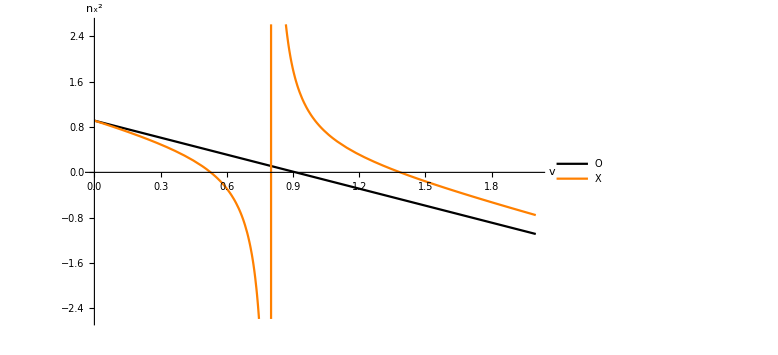

```mathematica
(*η=0*)
params={u->0.2,θ->0.3,η->0};
Plot[{Ο/.params,X/.params},{v,0,2},PlotStyle->{Black,Orange},PlotRange->{All,Automatic},PlotLegends->Placed[{"Ο","X"},Scaled[{0.7,0.7}]],ImageSize->Large,AxesLabel->{v,Subscript[n, x]^2},LabelStyle->{FontSize->20}]
(*SaveData["results/dispersionRelations/eta.png",%,"PNG"]*)
Clear[params];
```

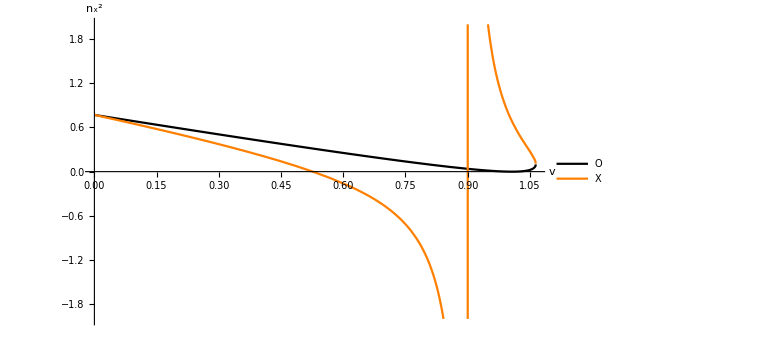

```mathematica
(*θ=0*)
params={u->0.1,θ->0,η->0.5};
Plot[{Ο/.params,X/.params},{v,0,2},PlotStyle->{Black,Orange},PlotRange->{All,{-2,2}},PlotLegends->Placed[{"Ο","X"},Scaled[{0.9,0.8}]],ImageSize->Large,AxesLabel->{v,Subscript[n, x]^2},LabelStyle->{FontSize->20}]
(*SaveData["results/dispersionRelations/teta.png",%,"PNG"]*)
Clear[params];
```

```mathematica
$Assumptions={-π/2<$θ<π/2,-π/2<$η<π/2,v>0,0<u<1};
ord=2/(2-((u-u Cos[θ]^2 Sin[η]^2)-√(u (u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4))));
ext=2/(2-((u-u Cos[θ]^2 Sin[η]^2)+√(u (u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4))));
Subscript[e, y^o]=(1-Cos[θ]^2 Sin[η]^2)(1-ord(1-u));
Subscript[e, z^o]=-Cos[θ]Sin[η](Sin[θ](1-ord(1-u))+ⅈ √u Cos[θ]Cos[η]);
Subscript[e, y^x]=(1-Cos[θ]^2 Sin[η]^2)(1-ext(1-u));
Subscript[e, z^x]=-Cos[θ]Sin[η](Sin[θ](1-ext(1-u))+ⅈ √u Cos[θ]Cos[η]);
Inverse[Subscript[Υ, vacuum]].({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, -Sin[$θ]Tan[$η], -(Sin[$θ]^2+Cos[$θ]^2 Cos[$η]^2)/(Cos[$θ]Cos[$η])}, {0, 0, Cos[$θ]/Cos[$η], Sin[$θ]Tan[$η]}}).({{Subscript[e, y^o], Subscript[e, y^x], -Subscript[e, y^o], -Subscript[e, y^x]}, {Subscript[e, z^o], Subscript[e, z^x], -Subscript[e, z^o], -Subscript[e, z^x]}, {Subscript[e, y^o], Subscript[e, y^x], Subscript[e, y^o], Subscript[e, y^x]}, {Subscript[e, z^o], Subscript[e, z^x], Subscript[e, z^o], Subscript[e, z^x]}})/.{θ->$θ,η->$η}//Simplify//MatrixForm
(%⟦{1,2},{1,2}⟧)/Det[%⟦{1,2},{1,2}⟧]//Simplify//MatrixForm
%/.$θ->0//Simplify//MatrixForm
```

```mathematica
Series[1-(2v(1-v))/(2(1-v)-u (1-Cos[θ]^2 Sin[η]^2)±√(u^2(1-Cos[θ]^2 Sin[η]^2)^2+4u(1-v)^2(Cos[θ]Sin[η])^2)),{v,0,1}]//Normal//Simplify
```

1+(2 v)/(-2+((u-u Cos[θ]^2 Sin[η]^2)±√(u (u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4))))

```mathematica
Inverse[({{-Sin[η], -Sin[θ]Cos[η], Cos[θ]Cos[η]}, {Cos[η], -Sin[θ]Sin[η], Cos[θ]Sin[η]}, {0, Cos[θ], Sin[θ]}})].({{Sin[θ], 0, Cos[θ]Sin[η]}, {0, 1, 0}, {-Cos[θ]Sin[η], 0, Sin[θ]}})//Simplify//MatrixForm
```

(-Sin[η] Sin[θ] | Cos[η] | -Cos[θ] Sin[η]^2
-Cos[η]^2 Cos[θ]^2 Sin[η]-Cos[θ]^2 Sin[η]^3-Cos[η] Sin[θ]^2 | -Sin[η] Sin[θ] | Cos[θ] (1-Cos[η] Sin[η]) Sin[θ]
Cos[θ] (Cos[η]-Sin[η]) Sin[θ] | Cos[θ] Sin[η] | Cos[η] Cos[θ]^2 Sin[η]+Cos[η]^2 Sin[θ]^2+Sin[η]^2 Sin[θ]^2)

```mathematica
Inverse[({{-Sin[η], -Sin[θ]Cos[η], Cos[θ]Cos[η]}, {Cos[η], -Sin[θ]Sin[η], Cos[θ]Sin[η]}, {0, Cos[θ], Sin[θ]}})].({{Sin[θ], 0, Cos[θ]Sin[η]}, {0, 1, 0}, {-Cos[θ]Sin[η], 0, Sin[θ]}}).({{√u}, {-ⅈ(1-ord(1-u))}, {ⅈ(√(1-Cos[θ]^2 Sin[η]^2))/(Cos[θ]Sin[η]) (1-ord(1-u))}})//FullSimplify//MatrixForm
```

$Aborted

```mathematica
({{-Sin[η] Sin[θ], Cos[η], -Cos[θ] Sin[η]^2}, {-Cos[η]^2 Cos[θ]^2 Sin[η]-Cos[θ]^2 Sin[η]^3-Cos[η] Sin[θ]^2, -Sin[η] Sin[θ], Cos[θ] (1-Cos[η] Sin[η]) Sin[θ]}, {Cos[θ] (Cos[η]-Sin[η]) Sin[θ], Cos[θ] Sin[η], Cos[η] Cos[θ]^2 Sin[η]+ Sin[θ]^2}})
```

```mathematica
({{Cos[θ] (Cos[η]-Sin[η]) Sin[θ], Cos[θ] Sin[η], Cos[η] Cos[θ]^2 Sin[η]+ Sin[θ]^2}}).({{√u}, {-ⅈ(1-ord(1-u))}, {ⅈ(√(1-Cos[θ]^2 Sin[η]^2))/(Cos[θ]Sin[η]) (1-ord(1-u))}})//FullSimplify//MatrixForm
```

(-1/2 ⅈ Cos[θ] Sin[η] (u-u Cos[θ]^2 Sin[η]^2+√(u (u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4)))+√u Cos[θ] (Cos[η]-Sin[η]) Sin[θ]+1/2 ⅈ Csc[η] Sec[θ] √(1-Cos[θ]^2 Sin[η]^2) (u-u Cos[θ]^2 Sin[η]^2+√(u (u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4))) (Cos[η] Cos[θ]^2 Sin[η]+Sin[θ]^2))

```mathematica
%121/.{θ->0.1,η->0.1,u->0.2}//N
```

{{0.0397669+0.204555 ⅈ}}

```mathematica
Inverse[({{-Sin[η], -Sin[θ]Cos[η], Cos[θ]Cos[η]}, {Cos[η], -Sin[θ]Sin[η], Cos[θ]Sin[η]}, {0, Cos[θ], Sin[θ]}})]
```

```mathematica
Inverse[({{-Sin[η], -Sin[θ]Cos[η], Cos[θ]Cos[η]}, {Cos[η], -Sin[θ]Sin[η], Cos[θ]Sin[η]}, {0, Cos[θ], Sin[θ]}})].({{0}, {1}, {0}})//Simplify
```

{{Cos[η]},{-Sin[η] Sin[θ]},{Cos[θ] Sin[η]}}

```mathematica
$Assumptions->{-π/2<θ<π/2,-π/2<η<π/2,0<u<1};
({{Cot[η], Sin[θ]}, {-Sin[θ], Cot[η]}}).({{(-2ⅈ √u Cos[β])/(√(4 u Cos[β]^2+(-u Sin[β]^2+√(u (4 Cos[β]^2+u Sin[β]^4)))^2)), (-2ⅈ √u Cos[β])/(√(4 u Cos[β]^2+(u Sin[β]^2+√(u (4 Cos[β]^2+u Sin[β]^4)))^2))}, {(u Sin[β]^2-√(u^2 Sin[β]^4+4u Cos[β]^2))/(√(4 u Cos[β]^2+(-u Sin[β]^2+√(u (4 Cos[β]^2+u Sin[β]^4)))^2)), (u Sin[β]^2+√(u^2 Sin[β]^4+4u Cos[β]^2))/(√(4 u Cos[β]^2+(u Sin[β]^2+√(u (4 Cos[β]^2+u Sin[β]^4)))^2))}});
%/√Det[%];
%/.{Sin[β]->√(1-Cos[θ]^2 Sin[η]^2),Cos[β]->Cos[θ]Sin[η]}//Simplify//MatrixForm
```

(-(16 (2 ⅈ √u Cos[η] Cos[θ]+(-u+u Cos[θ]^2 Sin[η]^2+√(u (u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4))) Sin[θ]))/(√(u (u+u Cos[θ]^4 Sin[η]^4-√(u (u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4))+Cos[θ]^2 Sin[η]^2 (4-2 u+√(u (u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4))))) √(-(ⅈ Cos[θ] (3+2 Cos[2 η] Cos[θ]^2-Cos[2 θ]) (64+41 u+8 u Cos[4 η] Cos[θ]^4+64 Cos[2 θ]-20 u Cos[2 θ]-16 Cos[2 η] Cos[θ]^2 (8-3 u+u Cos[2 θ])+3 u Cos[4 θ]) Csc[η] (3 u+2 u Cos[2 η] Cos[θ]^2-u Cos[2 θ]+4 √(u (u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4))))/(√(u (u+u Cos[θ]^4 Sin[η]^4-√(u (u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4))+Cos[θ]^2 Sin[η]^2 (4-2 u+√(u (u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4))))) (u+u Cos[θ]^4 Sin[η]^4+√(u (u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4))-Cos[θ]^2 Sin[η]^2 (-4+2 u+√(u (u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4))))^(3/2)))) | (16 (-2 ⅈ √u Cos[η] Cos[θ]+(u-u Cos[θ]^2 Sin[η]^2+√(u (u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4))) Sin[θ]))/(√(-(ⅈ Cos[θ] (3+2 Cos[2 η] Cos[θ]^2-Cos[2 θ]) (64+41 u+8 u Cos[4 η] Cos[θ]^4+64 Cos[2 θ]-20 u Cos[2 θ]-16 Cos[2 η] Cos[θ]^2 (8-3 u+u Cos[2 θ])+3 u Cos[4 θ]) Csc[η] (3 u+2 u Cos[2 η] Cos[θ]^2-u Cos[2 θ]+4 √(u (u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4))))/(√(u (u+u Cos[θ]^4 Sin[η]^4-√(u (u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4))+Cos[θ]^2 Sin[η]^2 (4-2 u+√(u (u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4))))) (u+u Cos[θ]^4 Sin[η]^4+√(u (u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4))-Cos[θ]^2 Sin[η]^2 (-4+2 u+√(u (u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4))))^(3/2))) √(u (u+u Cos[θ]^4 Sin[η]^4+√(u (u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4))-Cos[θ]^2 Sin[η]^2 (-4+2 u+√(u (u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4))))))
-(16 (u Cos[η] Cos[θ]^2 Sin[η]+Cot[η] (-u+√(u (u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4)))-2 ⅈ √u Cos[θ] Sin[η] Sin[θ]))/(√(u (u+u Cos[θ]^4 Sin[η]^4-√(u (u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4))+Cos[θ]^2 Sin[η]^2 (4-2 u+√(u (u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4))))) √(-(ⅈ Cos[θ] (3+2 Cos[2 η] Cos[θ]^2-Cos[2 θ]) (64+41 u+8 u Cos[4 η] Cos[θ]^4+64 Cos[2 θ]-20 u Cos[2 θ]-16 Cos[2 η] Cos[θ]^2 (8-3 u+u Cos[2 θ])+3 u Cos[4 θ]) Csc[η] (3 u+2 u Cos[2 η] Cos[θ]^2-u Cos[2 θ]+4 √(u (u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4))))/(√(u (u+u Cos[θ]^4 Sin[η]^4-√(u (u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4))+Cos[θ]^2 Sin[η]^2 (4-2 u+√(u (u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4))))) (u+u Cos[θ]^4 Sin[η]^4+√(u (u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4))-Cos[θ]^2 Sin[η]^2 (-4+2 u+√(u (u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4))))^(3/2)))) | (16 (-u Cos[η] Cos[θ]^2 Sin[η]+Cot[η] (u+√(u (u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4)))+2 ⅈ √u Cos[θ] Sin[η] Sin[θ]))/(√(-(ⅈ Cos[θ] (3+2 Cos[2 η] Cos[θ]^2-Cos[2 θ]) (64+41 u+8 u Cos[4 η] Cos[θ]^4+64 Cos[2 θ]-20 u Cos[2 θ]-16 Cos[2 η] Cos[θ]^2 (8-3 u+u Cos[2 θ])+3 u Cos[4 θ]) Csc[η] (3 u+2 u Cos[2 η] Cos[θ]^2-u Cos[2 θ]+4 √(u (u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4))))/(√(u (u+u Cos[θ]^4 Sin[η]^4-√(u (u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4))+Cos[θ]^2 Sin[η]^2 (4-2 u+√(u (u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4))))) (u+u Cos[θ]^4 Sin[η]^4+√(u (u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4))-Cos[θ]^2 Sin[η]^2 (-4+2 u+√(u (u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4))))^(3/2))) √(u (u+u Cos[θ]^4 Sin[η]^4+√(u (u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4))-Cos[θ]^2 Sin[η]^2 (-4+2 u+√(u (u-2 (-2+u) Cos[θ]^2 Sin[η]^2+u Cos[θ]^4 Sin[η]^4)))))))

```mathematica
Limit[%253,η->0]
```

{{√(-ⅈ √(Cos[θ]^2) Sec[θ]),0},{0,1/(√(-ⅈ √(Cos[θ]^2) Sec[θ]))}}

```mathematica
Assuming[{0<u<1,-π/2<θ<π/2},Simplify[%255]]//MatrixForm
```

(-(-1)^(3/4) | 0
0 | (-1)^(1/4))

```mathematica
Assuming[{-π/2<$θ<π/2,-π/2<$η<π/2,0<$u<1},Simplify[%253/.{η->$η,θ->$θ,u->$u}]]
```

{{-((16 √2 √Abs[Sin[$η]] ($u ($u-2 (-2+$u) Cos[$θ]^2 Sin[$η]^2+$u Cos[$θ]^4 Sin[$η]^4))^(1/4) (2 ⅈ √($u) Cos[$η] Cos[$θ]+(-$u+$u Cos[$θ]^2 Sin[$η]^2+√($u ($u-2 (-2+$u) Cos[$θ]^2 Sin[$η]^2+$u Cos[$θ]^4 Sin[$η]^4))) Sin[$θ]))/(√(-((ⅈ $u (3+2 Cos[2 $η] Cos[$θ]^2-Cos[2 $θ]) (64+41 $u+8 $u Cos[4 $η] Cos[$θ]^4+64 Cos[2 $θ]-20 $u Cos[2 $θ]-16 Cos[2 $η] Cos[$θ]^2 (8-3 $u+$u Cos[2 $θ])+3 $u Cos[4 $θ]) Csc[$η] (3 $u+2 $u Cos[2 $η] Cos[$θ]^2-$u Cos[2 $θ]+4 √($u ($u-2 (-2+$u) Cos[$θ]^2 Sin[$η]^2+$u Cos[$θ]^4 Sin[$η]^4))) ($u Cos[$θ]^4+Csc[$η]^4 ($u-√($u ($u-2 (-2+$u) Cos[$θ]^2 Sin[$η]^2+$u Cos[$θ]^4 Sin[$η]^4)))+Cos[$θ]^2 Csc[$η]^2 (4-2 $u+√($u ($u-2 (-2+$u) Cos[$θ]^2 Sin[$η]^2+$u Cos[$θ]^4 Sin[$η]^4)))))/($u Cos[$θ]^4+Csc[$η]^4 ($u+√($u ($u-2 (-2+$u) Cos[$θ]^2 Sin[$η]^2+$u Cos[$θ]^4 Sin[$η]^4)))-Cos[$θ]^2 Csc[$η]^2 (-4+2 $u+√($u ($u-2 (-2+$u) Cos[$θ]^2 Sin[$η]^2+$u Cos[$θ]^4 Sin[$η]^4)))))))),(16 √2 √Abs[Sin[$η]] ($u ($u-2 (-2+$u) Cos[$θ]^2 Sin[$η]^2+$u Cos[$θ]^4 Sin[$η]^4))^(1/4) (-2 ⅈ √($u) Cos[$η] Cos[$θ]+($u-$u Cos[$θ]^2 Sin[$η]^2+√($u ($u-2 (-2+$u) Cos[$θ]^2 Sin[$η]^2+$u Cos[$θ]^4 Sin[$η]^4))) Sin[$θ]))/(√(-ⅈ $u (3+2 Cos[2 $η] Cos[$θ]^2-Cos[2 $θ]) (64+41 $u+8 $u Cos[4 $η] Cos[$θ]^4+64 Cos[2 $θ]-20 $u Cos[2 $θ]-16 Cos[2 $η] Cos[$θ]^2 (8-3 $u+$u Cos[2 $θ])+3 $u Cos[4 $θ]) Csc[$η] (3 $u+2 $u Cos[2 $η] Cos[$θ]^2-$u Cos[2 $θ]+4 √($u ($u-2 (-2+$u) Cos[$θ]^2 Sin[$η]^2+$u Cos[$θ]^4 Sin[$η]^4)))))},{-((16 √2 √Abs[Sin[$η]] ($u ($u-2 (-2+$u) Cos[$θ]^2 Sin[$η]^2+$u Cos[$θ]^4 Sin[$η]^4))^(1/4) ($u Cos[$η] Cos[$θ]^2 Sin[$η]+Cot[$η] (-$u+√($u ($u-2 (-2+$u) Cos[$θ]^2 Sin[$η]^2+$u Cos[$θ]^4 Sin[$η]^4)))-2 ⅈ √($u) Cos[$θ] Sin[$η] Sin[$θ]))/(√(-((ⅈ $u (3+2 Cos[2 $η] Cos[$θ]^2-Cos[2 $θ]) (64+41 $u+8 $u Cos[4 $η] Cos[$θ]^4+64 Cos[2 $θ]-20 $u Cos[2 $θ]-16 Cos[2 $η] Cos[$θ]^2 (8-3 $u+$u Cos[2 $θ])+3 $u Cos[4 $θ]) Csc[$η] (3 $u+2 $u Cos[2 $η] Cos[$θ]^2-$u Cos[2 $θ]+4 √($u ($u-2 (-2+$u) Cos[$θ]^2 Sin[$η]^2+$u Cos[$θ]^4 Sin[$η]^4))) ($u Cos[$θ]^4+Csc[$η]^4 ($u-√($u ($u-2 (-2+$u) Cos[$θ]^2 Sin[$η]^2+$u Cos[$θ]^4 Sin[$η]^4)))+Cos[$θ]^2 Csc[$η]^2 (4-2 $u+√($u ($u-2 (-2+$u) Cos[$θ]^2 Sin[$η]^2+$u Cos[$θ]^4 Sin[$η]^4)))))/($u Cos[$θ]^4+Csc[$η]^4 ($u+√($u ($u-2 (-2+$u) Cos[$θ]^2 Sin[$η]^2+$u Cos[$θ]^4 Sin[$η]^4)))-Cos[$θ]^2 Csc[$η]^2 (-4+2 $u+√($u ($u-2 (-2+$u) Cos[$θ]^2 Sin[$η]^2+$u Cos[$θ]^4 Sin[$η]^4)))))))),(16 √2 √Abs[Sin[$η]] ($u ($u-2 (-2+$u) Cos[$θ]^2 Sin[$η]^2+$u Cos[$θ]^4 Sin[$η]^4))^(1/4) (-$u Cos[$η] Cos[$θ]^2 Sin[$η]+Cot[$η] ($u+√($u ($u-2 (-2+$u) Cos[$θ]^2 Sin[$η]^2+$u Cos[$θ]^4 Sin[$η]^4)))+2 ⅈ √($u) Cos[$θ] Sin[$η] Sin[$θ]))/(√(-ⅈ $u (3+2 Cos[2 $η] Cos[$θ]^2-Cos[2 $θ]) (64+41 $u+8 $u Cos[4 $η] Cos[$θ]^4+64 Cos[2 $θ]-20 $u Cos[2 $θ]-16 Cos[2 $η] Cos[$θ]^2 (8-3 $u+$u Cos[2 $θ])+3 $u Cos[4 $θ]) Csc[$η] (3 $u+2 $u Cos[2 $η] Cos[$θ]^2-$u Cos[2 $θ]+4 √($u ($u-2 (-2+$u) Cos[$θ]^2 Sin[$η]^2+$u Cos[$θ]^4 Sin[$η]^4)))))}}

```mathematica
%258/.{$θ->0}//Simplify//MatrixForm
```

(-(2 ⅈ √($u) √Abs[Sin[$η]] Cos[$η] ($u (16+3 $u+4 (-4+$u) Cos[2 $η]+$u Cos[4 $η]))^(1/4))/(√(-(ⅈ ($u (16+3 $u+4 (-4+$u) Cos[2 $η]+$u Cos[4 $η]))^(3/2) Cot[$η]^2 Csc[$η])/($u+Csc[$η]^4 ($u+√($u ($u-2 (-2+$u) Sin[$η]^2+$u Sin[$η]^4)))-Csc[$η]^2 (-4+2 $u+√($u ($u-2 (-2+$u) Sin[$η]^2+$u Sin[$η]^4)))))) | -(4 ⅈ √2 √($u) √Abs[Sin[$η]] Cos[$η] ($u ($u-2 (-2+$u) Sin[$η]^2+$u Sin[$η]^4))^(1/4))/(√(-ⅈ $u Cos[$η] (16+3 $u+4 (-4+$u) Cos[2 $η]+$u Cos[4 $η]) Cot[$η] ($u+$u Cos[2 $η]+2 √($u ($u-2 (-2+$u) Sin[$η]^2+$u Sin[$η]^4)))))
-(2^(3/4) √Abs[Sin[$η]] ($u ($u-2 (-2+$u) Sin[$η]^2+$u Sin[$η]^4))^(1/4) ($u Cos[$η] Sin[$η]+Cot[$η] (-$u+√($u ($u-2 (-2+$u) Sin[$η]^2+$u Sin[$η]^4)))))/(√(-(ⅈ ($u (16+3 $u+4 (-4+$u) Cos[2 $η]+$u Cos[4 $η]))^(3/2) Cot[$η]^2 Csc[$η])/($u+Csc[$η]^4 ($u+√($u ($u-2 (-2+$u) Sin[$η]^2+$u Sin[$η]^4)))-Csc[$η]^2 (-4+2 $u+√($u ($u-2 (-2+$u) Sin[$η]^2+$u Sin[$η]^4)))))) | (2 √2 √Abs[Sin[$η]] ($u ($u-2 (-2+$u) Sin[$η]^2+$u Sin[$η]^4))^(1/4) (-$u Cos[$η] Sin[$η]+Cot[$η] ($u+√($u ($u-2 (-2+$u) Sin[$η]^2+$u Sin[$η]^4)))))/(√(-ⅈ $u Cos[$η] (16+3 $u+4 (-4+$u) Cos[2 $η]+$u Cos[4 $η]) Cot[$η] ($u+$u Cos[2 $η]+2 √($u ($u-2 (-2+$u) Sin[$η]^2+$u Sin[$η]^4))))))